```mathematica
template ={"https://tools.wmflabs.org/xtools-articleinfo/?article=","&project=en.wikipedia.org"};
urlForm = Flatten @ Table[StringReplace[i, " "-> "_"], {i, Keys[compData]}];
TitleToEdit[article_] :=Block[{}, 
	(*Print[template[[1]]<> article <> template[[2]]]; *)
	Import[template[[1]]<> article <> template[[2]], "Data"]
]
```

```mathematica
editInfo = AssociationMap[TitleToEdit, urlForm];
```

```mathematica
DumpSave["/Users/ethan/Desktop/WSS2017/saved_data/editInfo.mx",editInfo];
```

```mathematica
<<"/Users/ethan/Desktop/WSS2017/saved_data/editInfo.mx"
```

```mathematica
For[i=0,i≤Length[urlForm],i++,
	If[editInfo[urlForm[[i]]==={}], Print[urlForm[[i]]], Nothing[]]
]
```

```mathematica
TotalRevisions[article_]:= editInfo[article][[2]][[1]][[1]][[4]][[2]]
```

```mathematica
NumEditors[article_]:=N[editInfo[article][[2]][[1]][[1]][[5]][[2]]]
```

```mathematica
revCount = AssociationMap[TotalRevisions,urlForm];
```

```mathematica
editorCount = AssociationMap[NumEditors,urlForm];
```

```mathematica
revPerEditor=Sort[revCount/editorCount,Greater];
```

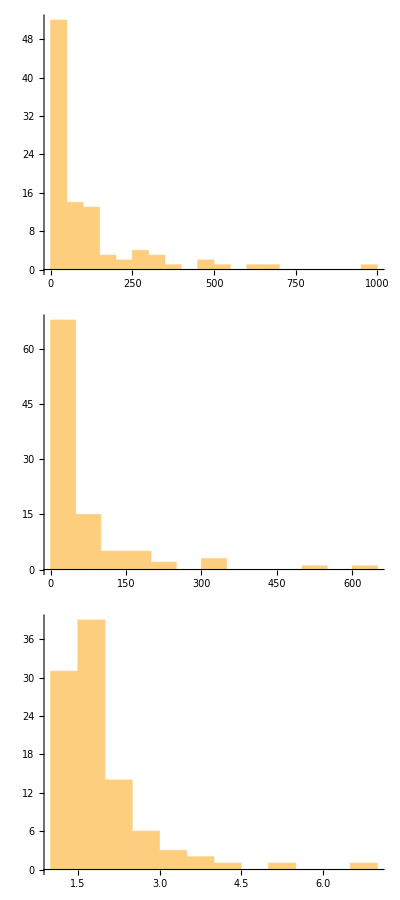

```mathematica
Histogram[#,ImageSize-> Large]&/@{revCount,editorCount,revPerEditor}//Column
```